```mathematica
ko01100=Import[NotebookDirectory[]<>"data/ko01100.xml"][[2]][[3]];
hsa00230=Import[NotebookDirectory[]<>"data/hsa00230.xml"][[2]][[3]];
hsa00240=Import[NotebookDirectory[]<>"data/hsa00240.xml"][[2]][[3]];
hsa00250=Import[NotebookDirectory[]<>"data/hsa00250.xml"][[2]][[3]];
hsa00260=Import[NotebookDirectory[]<>"data/hsa00260.xml"][[2]][[3]];
hsa00330=Import[NotebookDirectory[]<>"data/hsa00330.xml"][[2]][[3]];
hsa00480=Import[NotebookDirectory[]<>"data/hsa00480.xml"][[2]][[3]];
```

```mathematica
metaDataList={hsa00230,hsa00250,hsa00260,hsa00330,hsa00480,ko01100};
metaDataJoined=Join[hsa00230,hsa00250,hsa00260,hsa00330,hsa00480,ko01100];
```

```mathematica
nodeList=Table[Association/@Cases[metaDataList[[i]],XMLElement["entry",attr_,_]:>attr,Infinity],{i,Length[metaDataList]}];
nodes=Association/@Cases[metaDataJoined,XMLElement["entry",attr_,_]:>attr,Infinity];
nodes=DeleteDuplicates[nodes[[All,"name"]]];
ruleID2KID=Table[Table[nodeList[[i]][[j]]["id"]->nodeList[[i]][[j]][["name"]],{j,Length[nodeList[[i]]]}],{i,Length[metaDataList]}];
RelationData=Cases[metaDataJoined,
XMLElement[
"reaction",attr_,
{
XMLElement["substrate",substrateAttr_,_],
XMLElement["product",productAttr_,_]
}
]
:>Association[{"reaction"->attr,"substrate"->substrateAttr,"product"->productAttr}],Infinity];
edges=DeleteDuplicates[Map[Module[{substrate,product,type},
substrate="substrate"/. #;
product="product"/. #;
type="type"/. ("reaction"/. #);
If[type==="irreversible",substrate[[2]][[2]]->product[[2]][[2]],substrate[[2]][[2]]->product[[2]][[2]]]]&,RelationData]];
(*edgeList=Table[{Rule@@@RelationData[[i]][[All,{"entry1","entry2"}]]},{i,Length[metaDataList]}];
edges=Flatten[Table[edgeList[[i]]/.ruleID2KID[[i]],{i,Length[metaDataList]}]];*)
```

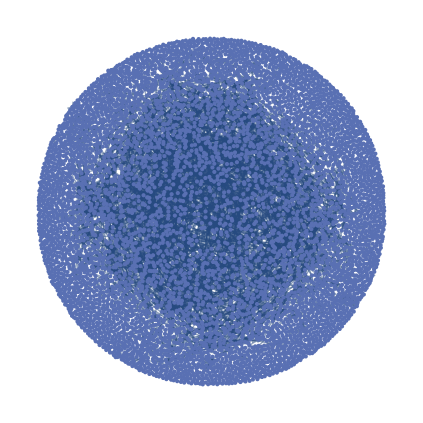

```mathematica
graph=Graph[nodes,edges,GraphLayout->"GravityEmbedding"]
```

```mathematica
selectedData=Import[NotebookDirectory[]<>"data/mapData.csv","Dataset","HeaderLines"->1];
GeneData=Import[NotebookDirectory[]<>"data/final_data.csv","Dataset","HeaderLines"->1];
selectedNodes=Rest[selectedData[All,"ID"]];
prefixedselectedNodes= Normal[StringJoin["cpd:",#]&/@selectedNodes];(*ruleID2KID=Table[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&][[i]]["id"]->StringTake[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&][[i]]["name"],{5,-1}],{i,Length[Select[entryData,MemberQ[Transpose[selectedData][[1]],StringTake[#[["name"]],{5,-1}]]&]]}];*)
ruleKID2Label=Table[Normal[StringJoin["cpd:",Normal[selectedData][[i]][[1]]]]->Normal[selectedData][[i]][[4]],{i,Length[selectedData]}];
```

```mathematica
GeneData
```

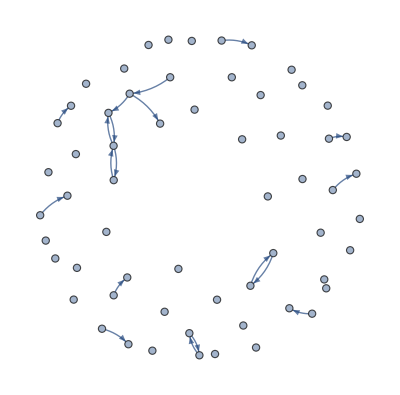

```mathematica
subgraph=Subgraph[graph,prefixedselectedNodes]
```

```mathematica
shortestPaths=Table[FindShortestPath[graph,prefixedselectedNodes[[i]],prefixedselectedNodes[[j]]],{i,Length[prefixedselectedNodes]},{j,i+1,Length[prefixedselectedNodes]}];
subgraphWithShortestPaths=Subgraph[graph,shortestPaths];
(*subgraph=FindSpanningTree[subgraphWithShortestPaths]*)
```

FindShortestPath::inv: The argument cpd:C00318 in FindShortestPath[Graph[<6632>, <3404>], cpd:C00018, cpd:C00318] is not a valid vertex.

FindShortestPath::inv: The argument cpd:C00670 in FindShortestPath[Graph[<6632>, <3404>], cpd:C00018, cpd:C00670] is not a valid vertex.

FindShortestPath::inv: The argument cpd:C02571 in FindShortestPath[Graph[<6632>, <3404>], cpd:C00018, cpd:C02571] is not a valid vertex.

General::stop: Further output of FindShortestPath::inv will be suppressed during this calculation.

```mathematica
name2CF["cpd:C00042"]
```

{#N/A,0.532068}

```mathematica
name2CF[name_]:={Normal[
Select[selectedData,#ID==StringSplit[name,":"][[2]]&][[1,"humanFC"]]],Normal[
Select[selectedData,#ID==StringSplit[name,":"][[2]]&][[1,"mouseFC"]]]}
cfHeatmap[name_]:={ColorData["Rainbow"][name2CF[name][[1]]/10+0.5],ColorData["Rainbow"][name2CF[name][[2]]/10+0.5]}
vfHeatmap[{xc_,yc_},name_,{w_,h_}]:=If[name2CF[name]!={"#N/A","#N/A"} ,{cfHeatmap[name][[1]],Rectangle[{xc-2w*4/3,yc-h*4/3},{xc,yc+h*4/3}],cfHeatmap[name][[2]],Rectangle[{xc,yc-h*4/3},{xc+2w*4/3,yc+h*4/3}]},{Circle[{xc,yc},h]}]
subgraph=Graph[FindSpanningTree@subgraphWithShortestPaths,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"output.svg",Graph[FindSpanningTree@subgraphWithShortestPaths,VertexShapeFunction->vfHeatmap,VertexLabels->ruleKID2Label,ImageSize->{2048/2,2048/2}]]
```

/home/maxwell-gao/Documents/MappingMetabolism/output.svg